Change this to point to the directory in which gro is installed.

```mathematica
SetDirectory["/Somewhere/On/Your/Computer/gro"];
```

## A simple example

Here’s how to call grong from Mathematica. The program dilute.gro takes two arguments, runs a simulation, and prints a Mathematica expression to standard output.

```mathematica
RunThrough["grong.app/Contents/MacOS/grong extras/dilute.gro 20 1000",""]
```

You can call grong with different outputs and Mathematica interprets the output to produce a list of histograms in this case.

```mathematica
Table[
Histogram[
RunThrough[
"grong.app/Contents/MacOS/grong extras/dilute.gro " 
<> ToString[20] <> " " <> ToString[i],""],
{10},AxesOrigin->{0,0},PlotRange->{{0,200},{0,50}}],
{i,1000, 2000, 250}]
```

## Tracking cell ids

```mathematica
data =RunThrough["grong.app/Contents/MacOS/grong extras/cell-tracker.gro 100 1.0",""];
```

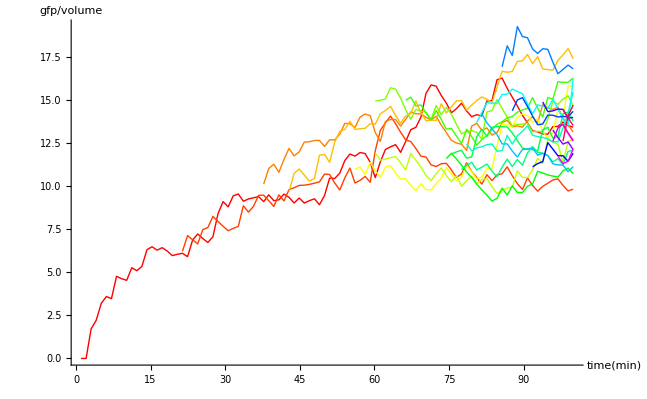

```mathematica
maxid = Max[Map[#⟦1⟧&,data]];
Show[Graphics[Table[
{Hue[i/maxid],
Line[Map[Take[#,-2]&,Select[data,#⟦1⟧==i&]]]},{i,0,maxid}]
],Axes->True,AspectRatio->1/GoldenRatio,AxesLabel->{"time(min)","gfp/volume"}]
```